0.7693332068822684336784353948877908796307461882534555470181500851352744799746663112113861201915917071608967639827528379851611747931853734939931164886311160072506769583364558885124191446095876755054056884117721509655409+0.070845813696600750809958947893102226247302467824297314312195791049686381356629857057212720706972345441496783302230609919120316620664138152701157291192227630003435054221354614358765235584746835948684880113830735434230532 x

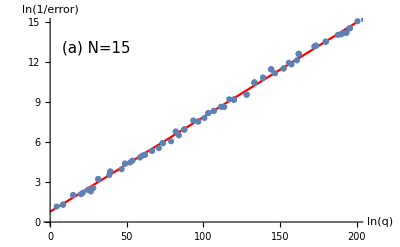

```mathematica
num =15;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
omega =Delete[nulist,num]/nulist[[num]];
orders = Range[5, 100, 1 ];
Elist =   Table[0,  Length[orders]];
qlist = Table[0,  Length[orders]];
For[s1 = 1, s1≤Length[orders], s1++, 
QQ = 10^orders[[s1]];
AA = Table[0,{i, 1,  num},{j,1,num}];
AA[[1, 1]] = 1; 
For[i=1, i ≤num-1, i++, AA[[1, i+1]]=Round[QQ*omega[[i]]];];
For[i=2, i≤num, i++, AA[[i,i]] = QQ; ];
bb = LatticeReduce[AA];
q = Abs[bb[[1,1]]];
qlist[[s1]] = q; 
error =Block[{$MaxExtraPrecision=1000}, N[Abs[q*omega - Round[q* omega ]], 220]];
Elist[[s1]] = Max[error];];
data = Table[{Log[qlist[[s1]]], -Log[Elist[[s1]]]},{s1, 1, Length[orders],1}];
pd = ListPlot[data, AxesLabel->{"ln(q)","ln(1/error)"},AxesStyle->15];
f = Fit[data, {1,x},x]
fd = Plot[f, {x, 0,200}, AxesLabel->{"ln(q)","ln(1/error)"},AxesStyle->15, PlotStyle-> RGBColor[1,0,0]];
ff = Show[ fd,pd];
t12 = Graphics[Text[Style["(a) N=15",15],{30,13}]];
t1 = Show[ff,t12]
```

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",t1,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",%973,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",%142,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling.eps",pd,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling.eps

```mathematica
omega
```

{(-1+√3)/(1+√3),(√2)/(1+√3),2/(1+√3),(√6)/(1+√3)}

```mathematica
Sin[Pi/12]
```

(-1+√3)/(2 √2)

```mathematica
N[1/14]
```

0.0714286

0.7319288861737941555240051528060474261143341353941757933728429562415696039310083307796096775875156472046653605098030318864651325124490613796650099106678390903938027327988737329508884264106651566528265883721627067471861+0.33417252445403109218932236212823450587523300347191362148116484404417672151462782590432922988198615799509664310454525423066736375820038241360921554434669482761849051483700200187686455309674616371659075139869312645927174 x

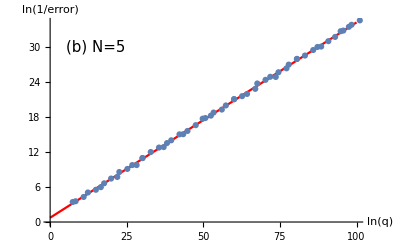

```mathematica
num =5;
nulist = 2 * Sin[Range[num]*Pi/2/(num+1)];
omega =Delete[nulist,num]/nulist[[num]];
orders = Range[5, 60, 1 ];
Elist =   Table[0,  Length[orders]];
qlist = Table[0,  Length[orders]];
For[s1 = 1, s1≤Length[orders], s1++, 
QQ = 10^orders[[s1]];
AA = Table[0,{i, 1,  num},{j,1,num}];
AA[[1, 1]] = 1; 
For[i=1, i ≤num-1, i++, AA[[1, i+1]]=Round[QQ*omega[[i]]];];
For[i=2, i≤num, i++, AA[[i,i]] = QQ; ];
bb = LatticeReduce[AA];
q = Abs[bb[[1,1]]];
qlist[[s1]] = q; 
error =Block[{$MaxExtraPrecision=1000}, N[Abs[q*omega - Round[q* omega ]], 220]];
Elist[[s1]] = Max[error];];
data = Table[{Log[qlist[[s1]]], -Log[Elist[[s1]]]},{s1, 1, Length[orders],1}];
pd = ListPlot[data, AxesLabel->{"ln(q)","ln(1/error)"},AxesStyle->15];
f = Fit[data, {1,x},x]
fd = Plot[f, {x, 0,100}, AxesLabel->{"ln(q)","ln(1/error)"},AxesStyle->15, PlotStyle-> RGBColor[1,0,0]];
ff = Show[fd, pd];
t12 = Graphics[Text[Style["(b) N=5",15],{15,30}]];
t2 = Show[ff,t12]
```

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
Export["E:\\L files\\2017_poincare_recurrence\\scaling2.eps",t2,"EPS"]
```

E:\L files\2017_poincare_recurrence\scaling2.eps

```mathematica
PacletInstall["D:\\My Downloads\\MaTex-1.7.0.paclet"]
```

Paclet[MaTeX,1.7.0,<>]

```mathematica
<<MaTex`
```

Get::noopen: Cannot open MaTex`.

$Failed

```mathematica
<<MaTeX`
```

The path to Ghostscipt is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

for documentation on configuring MaTeX.

```mathematica
ConfigureMaTeX[]
```

The path to Ghostscipt is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

for documentation on configuring MaTeX.

{pdfLaTeX→C:\CTEX\MiKTeX\miktex\bin\pdflatex.exe,Ghostscript→None,CacheSize→100}

```mathematica
ConfigureMaTex["Ghostscript" ->  "C:\\Program Files(x86)\\gs\\gs8.64\\bin\\gswin32c.exe"]
```

ConfigureMaTex[Ghostscript→C:\Program Files(x86)\gs\gs8.64\bin\gswin32c.exe]

```mathematica
ConfigureMaTex["Ghostscript"->"C:\\Program Files (x86)\\gs\\gs8.64\\bin\\gswin32c.exe"]
```

```mathematica
ConfigureMaTex["Ghostscript"->"C:\\Program Files (x86)\\gs\\gs8.64\\bin"]
```